2

4

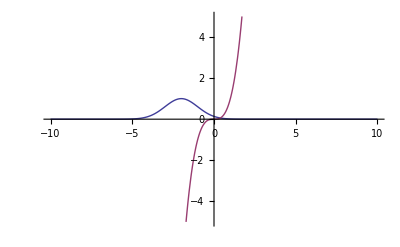

```mathematica
t=2
r=4
Plot[{Exp[-(u+t)^2/2],u^(r-1)},{u,-10,10},PlotRange->{{-10,10},{-5,5}}]
```

```mathematica
NIntegrate[Exp[-(u+t)^2/2]u^(r-1),{u,0,Infinity}]
```

0.013646

```mathematica
Pi
```

π

```mathematica
sol=N[2^(-r/2) ⅇ^(-t^2/2) Gamma[r] HypergeometricU[r/2,1/2,t^2/2]]
```

0.013646

```mathematica
Clear[t,r]
Integrate[2^(-r/2) ⅇ^(-t^2/2) Gamma[r] HypergeometricU[r/2,1/2,t^2/2] t^a,{t,xn,Infinity}]
```

2^(-r/2) Gamma[r] If[Re[a]>-1,√π ((2^(1/2 (-1+a)) Gamma[(1+a)/2] Hypergeometric2F1[(1+a)/2,r/2,1/2,1])/Gamma[(1+r)/2]+(2^(1/2 (-1+a)) (2+a+r) Gamma[1+a/2] Hypergeometric2F1[(2+a)/2,(1+r)/2,1/2,1])/((1+a) Gamma[1+r/2])-(xn^(1+a) HypergeometricPFQ[{1/2+a/2,1/2-r/2},{1/2,3/2+a/2},-xn^2/2])/((1+a) Gamma[(1+r)/2])+(√2 xn^(1+a) √(xn^2) HypergeometricPFQ[{1+a/2,1-r/2},{3/2,2+a/2},-xn^2/2])/((2+a) Gamma[r/2])),Integrate[ⅇ^(-t^2/2) t^a HypergeometricU[r/2,1/2,t^2/2],{t,xn,∞},Assumptions→Re[a]≤-1]]

```mathematica
sol2=Simplify[√π ((2^(1/2 (-1+a)) Gamma[(1+a)/2] Hypergeometric2F1[(1+a)/2,r/2,1/2,1])/Gamma[(1+r)/2]+(2^(1/2 (-1+a)) (2+a+r) Gamma[1+a/2] Hypergeometric2F1[(2+a)/2,(1+r)/2,1/2,1])/((1+a) Gamma[1+r/2])-(xn^(1+a) HypergeometricPFQ[{1/2+a/2,1/2-r/2},{1/2,3/2+a/2},-xn^2/2])/((1+a) Gamma[(1+r)/2])+(√2 xn^(1+a) √(xn^2) HypergeometricPFQ[{1+a/2,1-r/2},{3/2,2+a/2},-xn^2/2])/((2+a) Gamma[r/2]))]
```

√π ((2^(1/2 (-1+a)) Gamma[(1+a)/2] Hypergeometric2F1[(1+a)/2,r/2,1/2,1])/Gamma[(1+r)/2]+(2^(1/2 (-1+a)) (2+a+r) Gamma[1+a/2] Hypergeometric2F1[(2+a)/2,(1+r)/2,1/2,1])/((1+a) Gamma[1+r/2])-(xn^(1+a) HypergeometricPFQ[{1/2+a/2,1/2-r/2},{1/2,3/2+a/2},-xn^2/2])/((1+a) Gamma[(1+r)/2])+(√2 xn^(1+a) √(xn^2) HypergeometricPFQ[{1+a/2,1-r/2},{3/2,2+a/2},-xn^2/2])/((2+a) Gamma[r/2]))